```mathematica
?Options
```

Options[symbol] gives the list of default options assigned to a symbol. 
Options[expr] gives the options explicitly specified in a particular expression such as a graphics object. 
Options[stream] or Options[sname] gives options associated with a particular stream. 
Options[object] gives options associated with an external object such as a NotebookObject. 
Options[obj,name] gives the setting for the option name. 
Options[obj,{name_1,name_2,…}] gives a list of the settings for the options name_i.

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[{…,w[f_i],…},…] plots f_i with features defined by the symbolic wrapper w.
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.

```mathematica
??Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[{…,w[f_i],…},…] plots f_i with features defined by the symbolic wrapper w.
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.

Attributes[Plot]={Protected,ReadProtected}

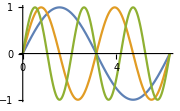

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions", ImageSize->Small]
```

```mathematica
?Map
```

Map[f,expr] or f/@expr applies f to each element on the first level in expr. 
Map[f,expr,levelspec] applies f to parts of expr specified by levelspec. 
Map[f] represents an operator form of Map that can be applied to an expression.

```mathematica
Sqrt[100]
```

10

```mathematica
range = Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
Map[Sqrt, range] // N
```

{1.,1.41421,1.73205,2.,2.23607,2.44949,2.64575,2.82843,3.,3.16228,3.31662,3.4641,3.60555,3.74166,3.87298,4.,4.12311,4.24264,4.3589,4.47214,4.58258,4.69042,4.79583,4.89898,5.,5.09902,5.19615,5.2915,5.38516,5.47723,5.56776,5.65685,5.74456,5.83095,5.91608,6.,6.08276,6.16441,6.245,6.32456,6.40312,6.48074,6.55744,6.63325,6.7082,6.78233,6.85565,6.9282,7.,7.07107,7.14143,7.2111,7.28011,7.34847,7.4162,7.48331,7.54983,7.61577,7.68115,7.74597,7.81025,7.87401,7.93725,8.,8.06226,8.12404,8.18535,8.24621,8.30662,8.3666,8.42615,8.48528,8.544,8.60233,8.66025,8.7178,8.77496,8.83176,8.88819,8.94427,9.,9.05539,9.11043,9.16515,9.21954,9.27362,9.32738,9.38083,9.43398,9.48683,9.53939,9.59166,9.64365,9.69536,9.74679,9.79796,9.84886,9.89949,9.94987,10.}

```mathematica
?Function
```

Function[body] or body& is a pure (or "anonymous") function. The formal parameters are # (or #1), #2, etc. 
Function[x,body] is a pure function with a single formal parameter x. 
Function[{x_1,x_2,…},body] is a pure function with a list of formal parameters. 
Function[params,body,attrs] is a pure function that is treated as having attributes attrs for purposes of evaluation.

```mathematica
?Slot
```

# represents the first argument supplied to a pure function. 
#n represents the n^th argument. 
#name represents the value associated with key "name" in an association in the first argument.

```mathematica
Function[#+1]
```

#1+1&

```mathematica
#+1&[3]
```

4

```mathematica
range = Range[12]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
Map[Function[#+1], range]
```

{2,3,4,5,6,7,8,9,10,11,12,13}

```mathematica
Function[#+1] /@ range
```

{2,3,4,5,6,7,8,9,10,11,12,13}

```mathematica
Map[#+1&, range ]
```

{2,3,4,5,6,7,8,9,10,11,12,13}

```mathematica
#+1&/@ range
```

{2,3,4,5,6,7,8,9,10,11,12,13}

```mathematica
range /. x_Integer ->x+1
```

{2,3,4,5,6,7,8,9,10,11,12,13}

```mathematica
Map[f, {1, 2, 3, {1, 2, 3}}]
```

{f[1],f[2],f[3],f[{1,2,3}]}

```mathematica
{1, 2, 3, {1, 2, 3}} /. n_integer->f[n]
```

{1,2,3,{1,2,3}}

```mathematica
nestedRange = Partition[range, 4]
```

{{1,2,3,4},{5,6,7,8},{9,10,11,12}}

```mathematica
?Join
```

Join[list_1,list_2,…] concatenates lists or other expressions that share the same head.
Join[list_1,list_2,…,n] joins the objects at level n in each of the list_i.

```mathematica
?Part
```

expr[[i]] or Part[expr,i] gives the i^th part of expr. 
expr[[-i]] counts from the end. 
expr[[i,j,…]] or Part[expr,i,j,…] is equivalent to expr[[i]][[j]]…. 
expr[[{i_1,i_2,…}]] gives a list of the parts i_1, i_2, … of expr. 
expr[[m;;n]] gives parts m through n.
expr[[m;;n;;s]] gives parts m through n in steps of s.
expr[[key]] gives the value associated with the key "key" in an association expr.
expr[[Key[k]]] gives the value associated with an arbitrary key k in the association expr.

```mathematica
Join[
#[[{-1}]],
#[[2;;-2]],
#[[{1}]]
]& /@ nestedRange
```

{{4,2,3,1},{8,6,7,5},{12,10,11,9}}

```mathematica
outcomes = Tuples[{Range[6], Range[6], Range[6]}]
```

{{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,2,1},{1,2,2},{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,3,1},{1,3,2},{1,3,3},{1,3,4},{1,3,5},{1,3,6},{1,4,1},{1,4,2},{1,4,3},{1,4,4},{1,4,5},{1,4,6},{1,5,1},{1,5,2},{1,5,3},{1,5,4},{1,5,5},{1,5,6},{1,6,1},{1,6,2},{1,6,3},{1,6,4},{1,6,5},{1,6,6},{2,1,1},{2,1,2},{2,1,3},{2,1,4},{2,1,5},{2,1,6},{2,2,1},{2,2,2},{2,2,3},{2,2,4},{2,2,5},{2,2,6},{2,3,1},{2,3,2},{2,3,3},{2,3,4},{2,3,5},{2,3,6},{2,4,1},{2,4,2},{2,4,3},{2,4,4},{2,4,5},{2,4,6},{2,5,1},{2,5,2},{2,5,3},{2,5,4},{2,5,5},{2,5,6},{2,6,1},{2,6,2},{2,6,3},{2,6,4},{2,6,5},{2,6,6},{3,1,1},{3,1,2},{3,1,3},{3,1,4},{3,1,5},{3,1,6},{3,2,1},{3,2,2},{3,2,3},{3,2,4},{3,2,5},{3,2,6},{3,3,1},{3,3,2},{3,3,3},{3,3,4},{3,3,5},{3,3,6},{3,4,1},{3,4,2},{3,4,3},{3,4,4},{3,4,5},{3,4,6},{3,5,1},{3,5,2},{3,5,3},{3,5,4},{3,5,5},{3,5,6},{3,6,1},{3,6,2},{3,6,3},{3,6,4},{3,6,5},{3,6,6},{4,1,1},{4,1,2},{4,1,3},{4,1,4},{4,1,5},{4,1,6},{4,2,1},{4,2,2},{4,2,3},{4,2,4},{4,2,5},{4,2,6},{4,3,1},{4,3,2},{4,3,3},{4,3,4},{4,3,5},{4,3,6},{4,4,1},{4,4,2},{4,4,3},{4,4,4},{4,4,5},{4,4,6},{4,5,1},{4,5,2},{4,5,3},{4,5,4},{4,5,5},{4,5,6},{4,6,1},{4,6,2},{4,6,3},{4,6,4},{4,6,5},{4,6,6},{5,1,1},{5,1,2},{5,1,3},{5,1,4},{5,1,5},{5,1,6},{5,2,1},{5,2,2},{5,2,3},{5,2,4},{5,2,5},{5,2,6},{5,3,1},{5,3,2},{5,3,3},{5,3,4},{5,3,5},{5,3,6},{5,4,1},{5,4,2},{5,4,3},{5,4,4},{5,4,5},{5,4,6},{5,5,1},{5,5,2},{5,5,3},{5,5,4},{5,5,5},{5,5,6},{5,6,1},{5,6,2},{5,6,3},{5,6,4},{5,6,5},{5,6,6},{6,1,1},{6,1,2},{6,1,3},{6,1,4},{6,1,5},{6,1,6},{6,2,1},{6,2,2},{6,2,3},{6,2,4},{6,2,5},{6,2,6},{6,3,1},{6,3,2},{6,3,3},{6,3,4},{6,3,5},{6,3,6},{6,4,1},{6,4,2},{6,4,3},{6,4,4},{6,4,5},{6,4,6},{6,5,1},{6,5,2},{6,5,3},{6,5,4},{6,5,5},{6,5,6},{6,6,1},{6,6,2},{6,6,3},{6,6,4},{6,6,5},{6,6,6}}

```mathematica
?Total
```

Total[list] gives the total of the elements in list. 
Total[list,n] totals all elements down to level n. 
Total[list,{n}] totals elements at level n. 
Total[list,{n_1,n_2}] totals elements at levels n_1 through n_2.

```mathematica
Total /@ outcomes
```

{3,4,5,6,7,8,4,5,6,7,8,9,5,6,7,8,9,10,6,7,8,9,10,11,7,8,9,10,11,12,8,9,10,11,12,13,4,5,6,7,8,9,5,6,7,8,9,10,6,7,8,9,10,11,7,8,9,10,11,12,8,9,10,11,12,13,9,10,11,12,13,14,5,6,7,8,9,10,6,7,8,9,10,11,7,8,9,10,11,12,8,9,10,11,12,13,9,10,11,12,13,14,10,11,12,13,14,15,6,7,8,9,10,11,7,8,9,10,11,12,8,9,10,11,12,13,9,10,11,12,13,14,10,11,12,13,14,15,11,12,13,14,15,16,7,8,9,10,11,12,8,9,10,11,12,13,9,10,11,12,13,14,10,11,12,13,14,15,11,12,13,14,15,16,12,13,14,15,16,17,8,9,10,11,12,13,9,10,11,12,13,14,10,11,12,13,14,15,11,12,13,14,15,16,12,13,14,15,16,17,13,14,15,16,17,18}

```mathematica
?Tally
```

Tally[list] tallies the elements in list, listing all distinct elements together with their multiplicities.
Tally[list,test] uses test to determine whether pairs of elements should be considered equivalent, and gives a list of the first representatives of each equivalence class, together with their multiplicities.

```mathematica
Tally[Total /@ outcomes]
```

{{3,1},{4,3},{5,6},{6,10},{7,15},{8,21},{9,25},{10,27},{11,27},{12,25},{13,21},{14,15},{15,10},{16,6},{17,3},{18,1}}

```mathematica
pdf = {#[[1]], #[[2]] / Length[outcomes]} & /@Tally{Total /@ outcomes}
```

{{3 Tally,4 Tally,5 Tally,6 Tally,7 Tally,8 Tally,4 Tally,5 Tally,6 Tally,7 Tally,8 Tally,9 Tally,5 Tally,6 Tally,7 Tally,8 Tally,9 Tally,10 Tally,6 Tally,7 Tally,8 Tally,9 Tally,10 Tally,11 Tally,7 Tally,8 Tally,9 Tally,10 Tally,11 Tally,12 Tally,8 Tally,9 Tally,10 Tally,11 Tally,12 Tally,13 Tally,4 Tally,5 Tally,6 Tally,7 Tally,8 Tally,9 Tally,5 Tally,6 Tally,7 Tally,8 Tally,9 Tally,10 Tally,6 Tally,7 Tally,8 Tally,9 Tally,10 Tally,11 Tally,7 Tally,8 Tally,9 Tally,10 Tally,11 Tally,12 Tally,8 Tally,9 Tally,10 Tally,11 Tally,12 Tally,13 Tally,9 Tally,10 Tally,11 Tally,12 Tally,13 Tally,14 Tally,5 Tally,6 Tally,7 Tally,8 Tally,9 Tally,10 Tally,6 Tally,7 Tally,8 Tally,9 Tally,10 Tally,11 Tally,7 Tally,8 Tally,9 Tally,10 Tally,11 Tally,12 Tally,8 Tally,9 Tally,10 Tally,11 Tally,12 Tally,13 Tally,9 Tally,10 Tally,11 Tally,12 Tally,13 Tally,14 Tally,10 Tally,11 Tally,12 Tally,13 Tally,14 Tally,15 Tally,6 Tally,7 Tally,8 Tally,9 Tally,10 Tally,11 Tally,7 Tally,8 Tally,9 Tally,10 Tally,11 Tally,12 Tally,8 Tally,9 Tally,10 Tally,11 Tally,12 Tally,13 Tally,9 Tally,10 Tally,11 Tally,12 Tally,13 Tally,14 Tally,10 Tally,11 Tally,12 Tally,13 Tally,14 Tally,15 Tally,11 Tally,12 Tally,13 Tally,14 Tally,15 Tally,16 Tally,7 Tally,8 Tally,9 Tally,10 Tally,11 Tally,12 Tally,8 Tally,9 Tally,10 Tally,11 Tally,12 Tally,13 Tally,9 Tally,10 Tally,11 Tally,12 Tally,13 Tally,14 Tally,10 Tally,11 Tally,12 Tally,13 Tally,14 Tally,15 Tally,11 Tally,12 Tally,13 Tally,14 Tally,15 Tally,16 Tally,12 Tally,13 Tally,14 Tally,15 Tally,16 Tally,17 Tally,8 Tally,9 Tally,10 Tally,11 Tally,12 Tally,13 Tally,9 Tally,10 Tally,11 Tally,12 Tally,13 Tally,14 Tally,10 Tally,11 Tally,12 Tally,13 Tally,14 Tally,15 Tally,11 Tally,12 Tally,13 Tally,14 Tally,15 Tally,16 Tally,12 Tally,13 Tally,14 Tally,15 Tally,16 Tally,17 Tally,13 Tally,14 Tally,15 Tally,16 Tally,17 Tally,18 Tally}}